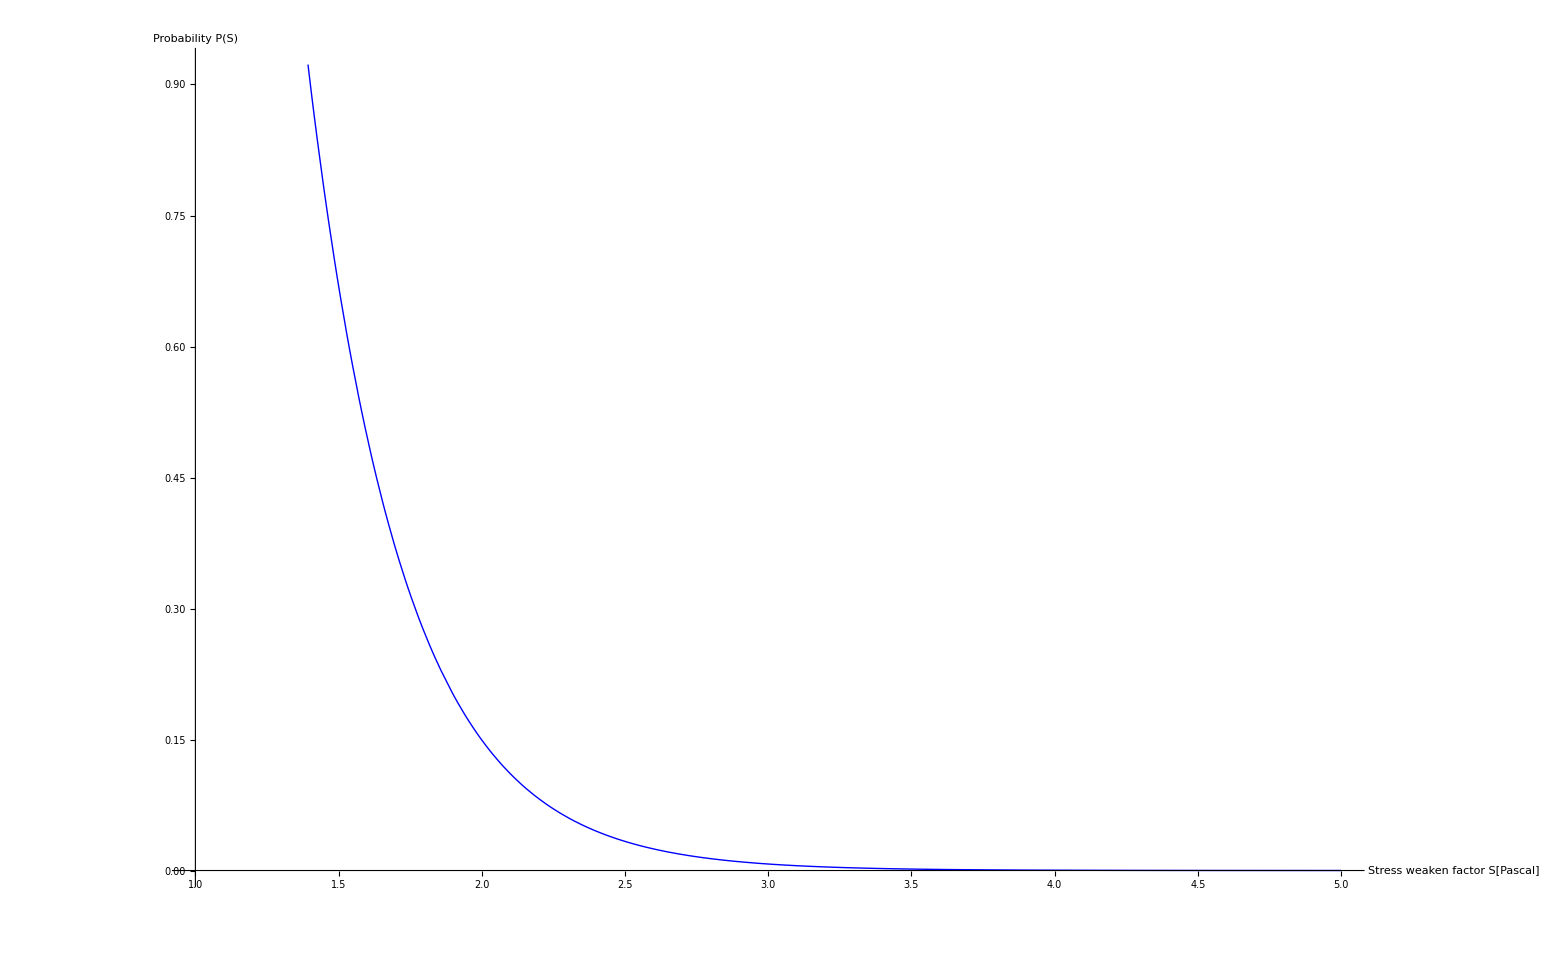

```mathematica
lam=3;
Smax=5;
c=lam/(Exp[-lam]-Exp[-lam*Smax]);
p=c*Exp[-lam*s];
Plot[p,{s,1,Smax},TicksStyle->Directive[Black,22],AxesStyle->Thick,AxesLabel->{Style["Stress weaken factor S[Pascal]",Black,24],Style["Probability P(S)",Black,24]},PlotStyle->{Blue,Thick}]
```